Вариант 5

Задание 1

```mathematica
Subscript[x, 0]=0;Subscript[x, 1]=Pi/4;Subscript[x, 2]=Pi/2;n=2;
f[x_]=(Cos[x]^3);
m=2;
NN=(m+1)(n+1)-1;
P[x_]=∑_(k=0)^NN Subscript[a, k] x^k;
eqv=Table[(D[P[x],{x,j}]//.x->Subscript[x, k])==(D[f[x],{x,j}]//.x->Subscript[x, k]),{j,0,m},{k,0,n}]//Flatten;
koef=Solve[eqv,{}]//Flatten;P[x_]=P[x]//.koef//N
```

1.-1.5 x^2+0.0182597 x^3+0.768144 x^4+0.255256 x^5-0.570733 x^6+0.210643 x^7-0.0238553 x^8

Задание 2, 3

```mathematica
Table[((D[P[x],{x,j}]//.x->Subscript[x, k])-(D[f[x],{x,j}]//.x->Subscript[x, k])//Chop)==0,{j,0,m},{k,0,n}]
```

{{True,True,True},{True,True,True},{True,True,True}}

```mathematica
Tbl=Table[{Subscript[x, i],Table[(D[f[x],{x,j}]//.x->Subscript[x, i]),{j,0,m}]},{i,0,n}];
```

```mathematica
P1[x_]=InterpolatingPolynomial[Tbl,x]//Expand;
N[P[x]-P1[x]]//Chop
```

0

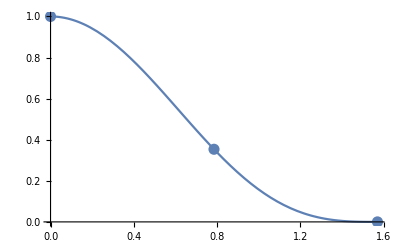

```mathematica
Tb=Table[{Subscript[x, i],f[Subscript[x, i]]},{i,0,n}];
Gr1=ListPlot[Tb,PlotStyle->{PointSize[0.02]}];
Gr2=Plot[P[x],{x,Subscript[x, 0],Subscript[x, n]}];
Show[Gr1,Gr2]
```

Задание 4

```mathematica
M1=Maximize[{D[f[x],{x,NN+1}],Subscript[x, 0]≤x≤Subscript[x, n]},x][[1]];
M2=Minimize[{D[f[x],{x,NN+1}],Subscript[x, 0]≤x≤Subscript[x, n]},x][[1]];
M=Max[{Abs[M1],Abs[M2]}];
ω[t_]=∏_(i=0)^n (t-Subscript[x, i])^(m+1);Subscript[M, ω]=Maximize[{Abs[ω[x]],Subscript[x, 0]≤x≤Subscript[x, n]},x][[1]];
R=M/((NN+1)!)Subscript[M, ω]//N
```

0.0000879336

Задание 5

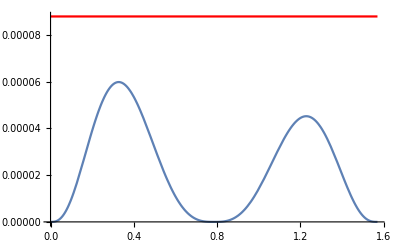

```mathematica
Gr3=Plot[Abs[f[x]-P[x]],{x,Subscript[x, 0],Subscript[x, n]}];
Gr4=Plot[R,{x,Subscript[x, 0],Subscript[x, n]},PlotStyle->Red];
Show[Gr3,Gr4,PlotRange->Automatic]
```

Задание 6

```mathematica
MR1=Maximize[{f[x]-P[x],Subscript[x, 0]≤x≤Subscript[x, n]},x][[1]];
MR2=Minimize[{f[x]-P[x],Subscript[x, 0]≤x≤Subscript[x, n]},x][[1]];
MR=Max[{Abs[MR1],Abs[MR2]}];
MR≤R
```

True

```mathematica
Unprotect[Power];
0^0:=1
Table[{f[x_]=x^j,f[x]==∑_(k=0)^NN Subscript[a, k] x^k//.(Solve[Table[(D[∑_(k=0)^NN Subscript[a, k] x^k,{x,j}]//.x->Subscript[x, k])==(D[f[x],{x,j}]//.x->Subscript[x, k]),{j,0,m},{k,0,n}]//Flatten,{}]//Flatten)},{j,0,NN+1}]
```

{{1,True},{x,True},{x^2,True},{x^3,True},{x^4,True},{x^5,True},{x^6,True},{x^7,True},{x^8,True},{x^9,x^9==-1/512 π^6 x^3+(9 π^5 x^4)/256-(33 π^4 x^5)/128+(63 π^3 x^6)/64-(33 π^2 x^7)/16+(9 π x^8)/4}}